```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/Users/zack/Documents/oscillators/snakingoscillators

#### Single trajectory runs

-Graphics- | -Graphics- | -Graphics-

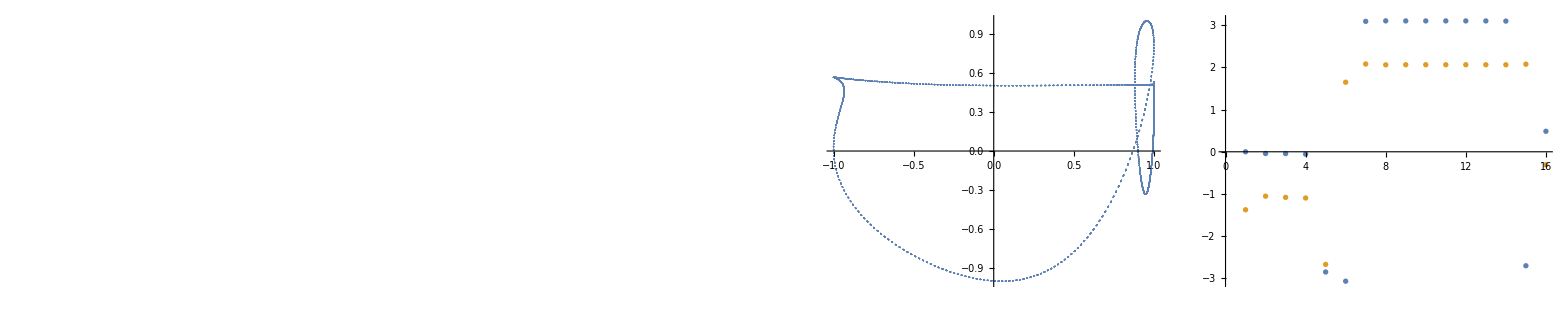

{1398,0.304284,36.9379}

```mathematica
filebase="data/chimeras/4";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
Grid[{{rasterizeBackground[ListDensityPlot[theta[[1;;1000]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;1000]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[orders,ImageSize->300]]}}]

phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
norms=Norm[#-dphases[[-1]]]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
If[Length[periods]>0,
period=Round[Mean[periods]];
Grid[{{rasterizeBackground[ListDensityPlot[dphases[[1;;period,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;period,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[Length[periods]>0,{period,Mean[orders[[-period;;-1]]],Norm[Differences[dphases[[-period+1;;-1]]],2]}]
```

#### Chimeras from random initial conditions

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]/100}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
dorder=0.01;
dperiod=0.01;
dnorm=0.25;
{bins,array}=HistogramList[vals[[All,2;;4]],{{dorder*(Range[1/dorder]-1)},{dperiod*(Range[3/dperiod]-1)},{0.1+dnorm*(Range[2/dnorm]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
SortBy[{#[[1]],#[[2]],#[[3]]*300,#[[4]]*100}&/@uniq,{#[[2]],#[[3]],#[[4]]}&]

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
Last/@ArrayRules[array][[1;;-2]]
```

29

{{130,5.56697×10^-17,3.,13.0291},{93,0.151249,148.4,27.6653},{217,0.265035,148.4,26.8898},{701,0.304285,139.85,36.4374},{401,0.355915,301.65,31.3999},{18,0.416209,151.,20.8428},{180,0.417377,148.5,21.6925},{596,0.423199,150.3,23.7557},{682,0.429572,148.6,30.8978},{907,0.433736,149.8,19.5188},{247,0.462668,148.4,19.4481},{612,0.467333,150.8,19.2639},{785,0.470831,149.8,19.0408},{411,0.492706,148.4,34.3712},{387,0.492707,148.4,35.0136},{614,0.506507,150.8,17.4768},{260,0.507702,148.5,16.6166},{658,0.509228,139.85,31.7435},{815,0.516831,148.6,31.8886},{816,0.533187,150.6,14.8315},{545,0.534704,148.4,14.0472},{31,0.546702,141.8,11.7642},{843,0.54815,140.6,10.8803},{725,0.59355,150.3,26.3987},{922,0.602228,148.65,31.6406},{59,0.678674,150.3,26.573},{407,0.680316,150.3,24.6157},{813,0.687482,148.7,28.7203},{368,0.773609,150.3,22.0584}}

{1,1,4,1,1,2,1,2,1,13,11,2,1,1,1,1,17,8,16,34,8,14,11,2,42,2,89,4,254}

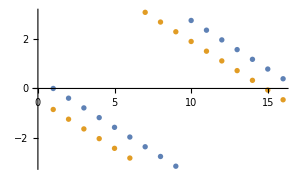
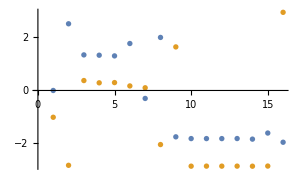
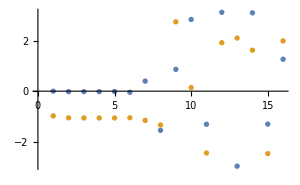
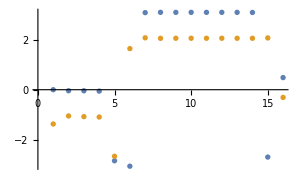
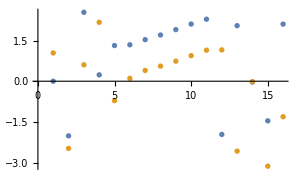
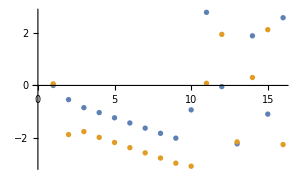
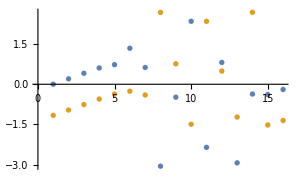
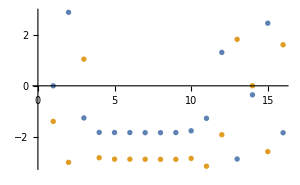
1 | 1.10947×10^-16 | 3. | 11.2397 | {6.28319,6.28319} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2 | 0.151252 | 148.4 | 27.9027 | {-4.84364,4.86058} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.265018 | 148.4 | 27.0865 | {-8.4679,8.48061} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.304284 | 139.85 | 37.2027 | {-1.65844,1.6899} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 0.355906 | 301.6 | 31.307 | {14.2726,-18.0871} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.417369 | 148.5 | 21.6078 | {16.0063,-10.7216} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.416197 | 150.9 | 21.0074 | {-13.1368,10.7301} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 0.42962 | 223.05 | 37.5695 | {-15.2262,15.2374} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 0.423202 | 150.3 | 24.1091 | {12.0438,-12.0355} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 0.433716 | 149.8 | 19.5281 | {8.8837,-4.45443} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
11 | 0.462647 | 148.4 | 19.453 | {-0.893364,5.2501} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
12 | 0.467338 | 150.9 | 19.1371 | {-11.7045,6.99936} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
13 | 0.47082 | 149.8 | 19.0716 | {-0.868237,5.25976} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
14 | 0.492695 | 148.4 | 34.6943 | {-1.81637,1.8206} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
15 | 0.492696 | 148.4 | 34.855 | {1.82483,-1.80366} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
16 | 0.509228 | 139.85 | 31.6547 | {-1.64495,1.6899} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
17 | 0.507703 | 148.5 | 16.7904 | {8.73299,-3.45681} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
18 | 0.506522 | 150.8 | 17.6635 | {-8.64146,3.38325} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
19 | 0.516814 | 148.65 | 32.7043 | {11.4762,-11.4593} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
20 | 0.534699 | 148.4 | 14.1298 | {5.06804,0.156656} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
21 | 0.533197 | 150.6 | 14.8961 | {-0.1794,-5.04824} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
22 | 0.548152 | 140.6 | 10.8803 | {1.29596,3.19522} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
23 | 0.54669 | 141.8 | 11.778 | {-3.15045,-1.34703} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
24 | 0.593559 | 150.3 | 26.1828 | {4.81167,-4.74897} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
25 | 0.602212 | 148.65 | 32.0482 | {7.83814,-7.82546} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
26 | 0.678644 | 150.3 | 26.733 | {1.17052,-1.14544} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
27 | 0.687482 | 148.7 | 29.8981 | {-4.21696,4.22541} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
28 | 0.680312 | 150.3 | 24.7045 | {1.18306,-1.14962} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
29 | 0.773606 | 150.3 | 22.682 | {0.58108,-0.576899} | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
phases2=Transpose[Catenate[{-Reverse[Transpose[phi]],-Reverse[Transpose[theta]]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
dphases2=(#-#[[1]]&/@phases2);
test=Mean[{Total[Mod[#[[1;;M]]-RotateLeft[#[[1;;M]]]+Pi,2*Pi]-Pi],Total[Mod[#[[M+1;;-1]]-RotateLeft[#[[M+1;;-1]]]+Pi,2*Pi]-Pi]}&/@dphases[[-Round[period/0.1];;-1]]];
If[period>0,
{Grid[{{j,order,period,norm,test,rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

```mathematica
{Grid[{{j,order,period,norm,rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}
```

{51 | 0.773606 | 150.3 | 22.682 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-}

{0.58108,-0.576899}

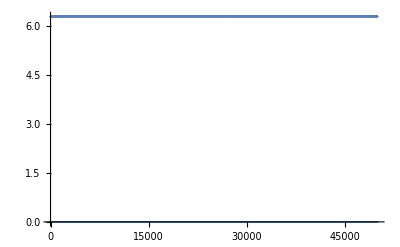

```mathematica
ListPlot[Total[Mod[#[[1;;M]]-RotateLeft[#[[1;;M]]]+Pi,2*Pi]-Pi]&/@dphases,PlotRange->All]
```

```mathematica
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
phases2=Transpose[Catenate[{-Reverse[Transpose[phi]],-Reverse[Transpose[theta]]}]];
dphases=(#-#[[1]]&/@phases);
dphases2=(#-#[[1]]&/@phases2);
rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]]
rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]]
```

-Graphics-

-Graphics-

#### Plot auto results

12

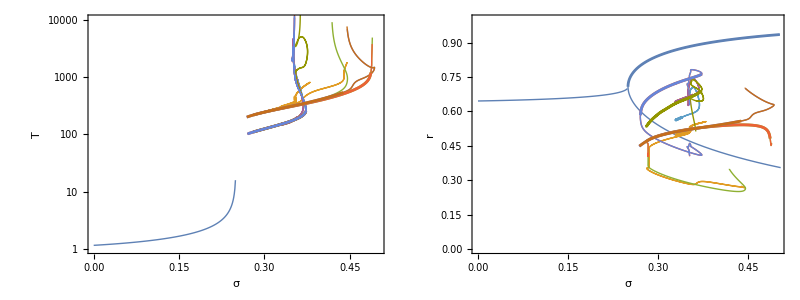

diagram.pdf

```mathematica
branches={DeleteCases[Import["auto/rel/steady.dat"],{}]};
stables={DeleteCases[DeleteCases[Import["auto/rel/steady.dat"],{}],u_/;u[[5]]<62]};
Monitor[Do[
If[FileExistsQ["auto/rel/"<>ToString[i]<>"fw.dat"]&&FileExistsQ["auto/rel/"<>ToString[i]<>"rv.dat"],
branch=Catenate[{Reverse[DeleteCases[Import["auto/rel/"<>ToString[i]<>"rv.dat"],{}]],DeleteCases[Import["auto/rel/"<>ToString[i]<>"fw.dat"],{}]}];AppendTo[branches,branch];
AppendTo[stables,DeleteCases[branch,u_/;u[[5]]<62]]];,{i,29,41}],i]
inds=First/@Position[Length/@branches,u_/;u>4];
sigmas=Range[0,0.25-0.001,0.001];
orders=Table[Mean[(1/(1+0.25*(1+4*sigma-((1-4*sigma)*(3+4*sigma))^0.5*Tan[(2*Pi/(0.75-2*sigma-4*sigma^2)^0.5*Range[0,100]/100*0.25*((1-4*sigma)*(3+4*sigma))^0.5)])^2)^0.5)],{sigma,sigmas}];
Length[inds]
p=Grid[{{Show[ListLogPlot[Transpose[{sigmas,1/(0.75-2*sigmas-4*sigmas^2)^0.5}],PlotRange->{{0,0.5},{10^0,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[1]]],ListLogPlot[branches[[inds,All,{1,3}]],PlotRange->{{0.25,0.5},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[1]]],ListLogPlot[stables[[inds,All,{1,3}]],PlotRange->{{0.25,0.5},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2]]]],Show[ListPlot[Transpose[{sigmas,orders}],PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[1]]],ListPlot[branches[[inds,All,{1,4}]],PlotRange->{{0.25,0.5},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[1]]],ListPlot[stables[[inds,All,{1,4}]],PlotRange->{{0.25,0.5},All},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2]]]]}}]
Export["diagram.pdf",p]
```